```mathematica
Get["fisr.m"]
Get["para.m"]
```

fisr: A Mathematica package for QED ISR structure function

by Yang Ma and Yongcheng Wu (April 2021)

If you use fisr in your research, please cite

• T. Han, Y. Ma, and K. Xie, Phys.Rev.D 103 (2021) 3, L031301, arXiv:2007.14300.

para: A Mathematica package for inputting Standard Model parameters

by Yang Ma (March 2020)

If you use para in your research, please cite

• T. Han, Y. Ma, and K. Xie, Phys.Rev.D 103 (2021) 3, L031301, arXiv:2007.14300.

## Plot ISR structure functions

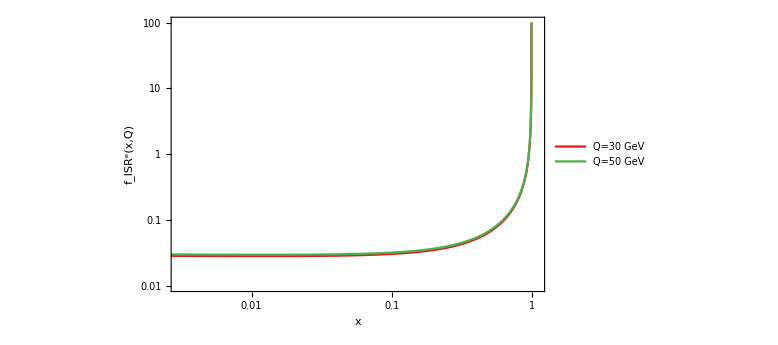

```mathematica
LogLogPlot[{fisr[x,30,ME]/.α-> αE/.SMinput,fisr[x,50,ME]/.α-> αE/.SMinput},{x,0,1},PlotStyle->{{c1},{c2},{c3},{c4}},PlotRange->{{0.003,1.1},{10^-2,10^2}},FrameLabel->{"x","f_ISR^e(x,Q)"},PlotLegends->Placed[LineLegend[{"Q=30 GeV","Q=50 GeV"},LegendLayout->{"Column",1}],{0.2,0.6}]]
```

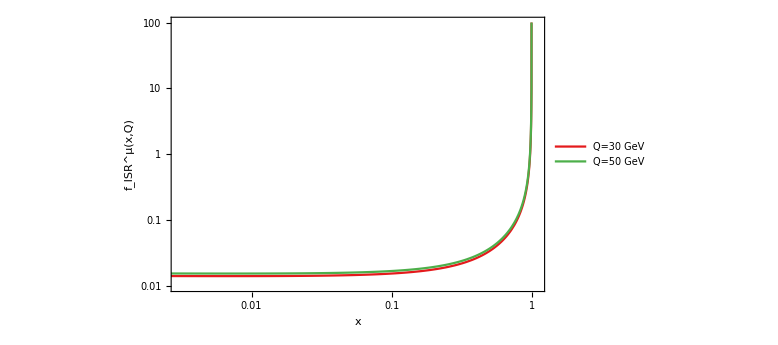

```mathematica
LogLogPlot[{fisr[x,30,MM]/.α-> αE/.SMinput,fisr[x,50,MM]/.α-> αE/.SMinput},{x,0,1},PlotStyle->{{c1},{c2},{c3},{c4}},PlotRange->{{0.003,1.1},{10^-2,10^2}},FrameLabel->{"x","f_ISR^μ(x,Q)"},PlotLegends->Placed[LineLegend[{"Q=30 GeV","Q=50 GeV"},LegendLayout->{"Column",1}],{0.2,0.6}]]
```

## Cross check with some typical SM processes

```mathematica
Get["ME2.m"]
```

ME2: Amplitude square after phase space integration

by Yang Ma (July 2020)

```mathematica
Lmd[x_,y_,z_]:=x^2-2 x y-2 x z+y^2-2 y z+z^2;
t2Cth=Simplify[{t->m1^2+m3^2-1/(2 s) ((m1^2-m2^2+s) (m3^2-m4^2+s)-Cth √Lmd[s,m1^2,m2^2] √Lmd[s,m3^2,m4^2])}/.{m1-> 0,m2-> 0,m3-> Mt,m4->Mt},s>Mt^2];
CSfactor[s_,m1_,m2_,m3_,m4_]:=1/(32 π s) (√Lmd[s,m3^2,m4^2])/(√Lmd[s,m1^2,m2^2])
CSfactor1=3894 10^5(CSfactor[s,0,0,Mt,Mt]//Simplify[#,s>Mt^2]&);
CSfactor2=3894 10^5(CSfactor[s,0,0,MZ,MH]//Simplify[#,s>MH^2&&s>MZ^2]&);
xStt[EE_]:=(CSfactor1/.SMinput/.s-> EE^2) ME2tt/.SMinput/.s->EE^2 
xSww[EE_]:=(CSfactor1/.Mt-> MW/.SMinput/.s-> EE^2) ME2ww/.SMinput/.s->EE^2 
xSzz[EE_]:=(CSfactor1/2/.Mt-> MZ/.SMinput/.s-> EE^2) ME2zz/.SMinput/.s->EE^2 
xSzh[EE_]:=(CSfactor2/.SMinput/.s-> EE^2) ME2zh/.SMinput/.s->EE^2
```

### Cross sections without ISR at Ecm =400 GeV (in pb)

```mathematica
Clear[EE];
EE=400;
```

```mathematica
(* cross section in pb *)
xStt[EE]//N[#,6]&
xSww[EE]//N[#,6]&
xSzz[EE]//N[#,6]&
xSzh[EE]//N[#,6]&
```

0.623138

9.60127

0.567014

0.0950728

### Cross sections with ISR

```mathematica
τ0tt=(4 Mt^2)/sMother;τ0ww=(4 MW^2)/sMother;τ0zh=(MZ+MH)^2/sMother;τ0zz=(4 MZ^2)/sMother;
fm2m[x_,Q_]:=fisr[x,Q,MM]
gm2m[x_,Q_]:=gisr[x,Q,MM]
mmLumi[x1_,x2_,Q_]:= fm2m[x1,Q] fm2m[x2,Q]/.α-> 1/137
mmLumi2[x1_,x2_,Q_]:= gm2m[x1,Q] gm2m[x2,Q]/.α->1/137
eeLumi[x1_,x2_,Q_]:= fm2m[x1,Q] fm2m[x2,Q]/.MM-> ME/.α->1/137
mmisr[ME2_,EE_,τ0_]:=Module[{jaco,Q=EE,x,y},x=1-(1-y)^(π/(αE (Log[Q^2/MM^2]-1)));jaco=π/(αE (Log[Q^2/MM^2]-1))(1-y)^(π/(αE (Log[Q^2/MM^2]-1))-1);NIntegrate[Piecewise[{{0,(x/.y-> y1) (x/.y-> y2)<τ0/.SMinput/.sMother-> EE^2}},(jaco/.y-> y1)(jaco/.y-> y2)mmLumi[x/.y-> y1,x/.y-> y2,Q] ME2/.s->((x/.y-> y1) (x/.y-> y2) sMother)/.SMinput/.sMother-> EE^2],{y1,0,1},{y2,0,1}]]
eeisr[ME2_,EE_,τ0_]:=Module[{jaco,Q=EE,x,y},x=1-(1-y)^(π/(αE (Log[Q^2/ME^2]-1)));jaco=π/(αE (Log[Q^2/ME^2]-1))(1-y)^(π/(αE (Log[Q^2/ME^2]-1))-1);NIntegrate[Piecewise[{{0,(x/.y-> y1) (x/.y-> y2)<τ0/.SMinput/.sMother-> EE^2}},(jaco/.y-> y1)(jaco/.y-> y2)eeLumi[x/.y-> y1,x/.y-> y2,Q] ME2/.s->((x/.y-> y1) (x/.y-> y2) sMother)/.SMinput/.sMother-> EE^2],{y1,0,1},{y2,0,1}]]
```

#### Check with 2007.14300

```mathematica
(* √s in TeV, cross section in fb *)
```

```mathematica
tabEE={3,6,10,14,30};
title={"√s","ww","tt","zz","zh"};
mm=Table[{tabEE[[n]],1000 mmisr[(CSfactor1/.Mt-> MW) ME2ww,1000tabEE[[n]],τ0ww/.SMinput],1000 mmisr[CSfactor1 ME2tt,1000tabEE[[n]],τ0tt/.SMinput],1000 mmisr[(CSfactor1/.Mt-> MZ) ME2zz,1000tabEE[[n]],τ0zz/.SMinput],1000 mmisr[CSfactor2 ME2zh,1000tabEE[[n]],τ0zh/.SMinput]},{n,1,tabEE//Length}]//Quiet;
ee=Table[{tabEE[[n]],1000 eeisr[(CSfactor1/.Mt-> MW) ME2ww,1000tabEE[[n]],τ0ww/.SMinput],1000 eeisr[CSfactor1 ME2tt,1000tabEE[[n]],τ0tt/.SMinput],1000 eeisr[(CSfactor1/.Mt-> MZ) ME2zz,1000tabEE[[n]],τ0zz/.SMinput],1000 eeisr[CSfactor2 ME2zh,1000tabEE[[n]],τ0zh/.SMinput]},{n,1,tabEE//Length}]//Quiet;
```

```mathematica
Insert[ee,title,1]//MatrixForm
```

(√s | ww | tt | zz | zh
3 | 584.518 | 25.4882 | 65.5834 | 2.05287
6 | 191.249 | 7.08562 | 21.4162 | 0.566342
10 | 82.1402 | 2.75796 | 9.18964 | 0.220034
14 | 46.7179 | 1.48205 | 5.22426 | 0.118165
30 | 12.7852 | 0.363628 | 1.4292 | 0.0289653)

```mathematica
Insert[mm,title,1]//MatrixForm
```

(√s | ww | tt | zz | zh
3 | 542.716 | 23.2424 | 60.8212 | 1.80697
6 | 174.809 | 6.29161 | 19.5551 | 0.486626
10 | 74.2561 | 2.40526 | 8.29983 | 0.186065
14 | 41.9375 | 1.27818 | 4.68551 | 0.0989242
30 | 11.3056 | 0.306333 | 1.26072 | 0.0237424)